```mathematica
d=//
	importStringTSV//
	DeleteCases[{}]//
	slice[All,{1,2}]//
	Cases[{_?NumericQ..}];
```

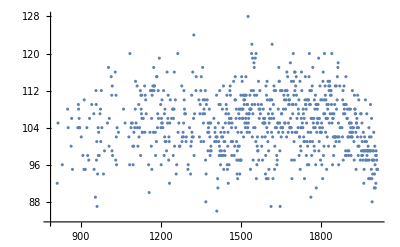

```mathematica
d//ListPlot
```

```mathematica
bezierFunction[data_]:=With[{f=BezierFunction[data],minMax=MinMax[data[[All,1]]]},
	Function[f[Rescale[Clip[#,minMax],minMax]][[2]]]
]
```

```mathematica
bezierFunction[d][1400]
```

105.271

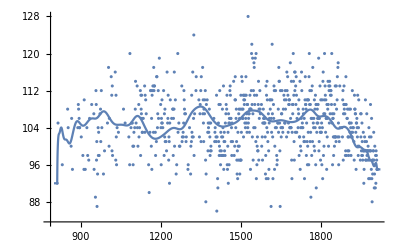

```mathematica
Show[
	ListPlot[d],
	Plot[bezierFunction[d][y],{y,800,2021}]
]
```

```mathematica
splineFunction[data_]:=With[{f=BSplineFunction[data],minMax=MinMax[data[[All,1]]]},
	Function[f[Rescale[Clip[#,minMax],minMax]][[2]]]
]
```

```mathematica
splineFunction[d][1400]
```

108.987

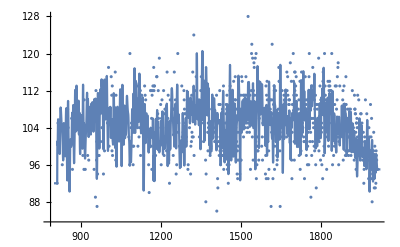

```mathematica
Show[
	ListPlot[d],
	Plot[splineFunction[d][y],{y,800,2021}]
]
```